```mathematica
axioms=ResourceFunction["https://www.wolframcloud.com/obj/wolframphysics/AxiomaticTheoryTWP"]["GroupAxioms"]
```

{a_∘(b_∘c_)<->(a_∘b_)∘c_,a_∘1<->a_,a_∘OverBar[a_]<->1}

```mathematica
{{"[◼]", "TwoWayRuleNestGraph"}}[x_∘ y_<->(y_∘x_)∘y_,a∘b,3,GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/4,VertexStyle->_->FontSize->13]
```

-Graphics-

```mathematica
Table[{{"[◼]", "BranchialGraph"}}@{{"[◼]", "TwoWayRuleNestGraph"}}[x_∘ y_<->(y_∘x_)∘y_,a∘b,t,],{t,3,4}]
```

{-Graphics-,-Graphics-}


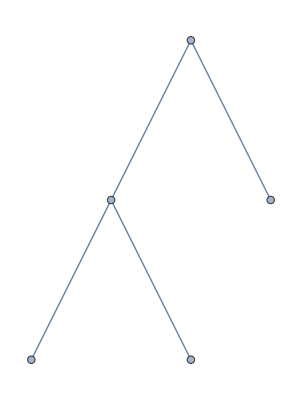
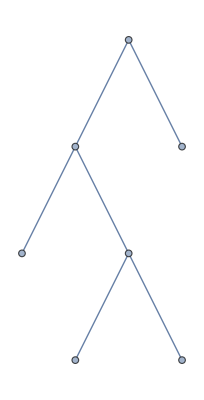
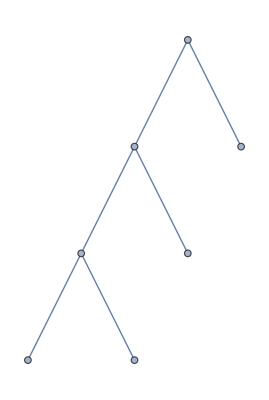
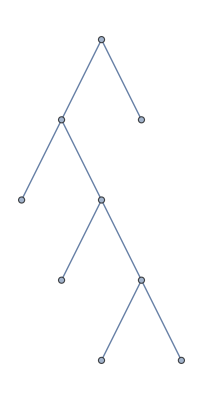
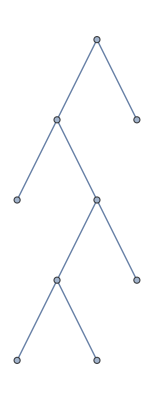
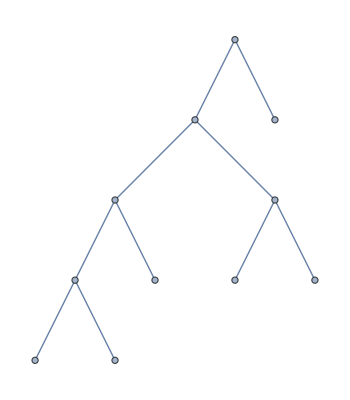
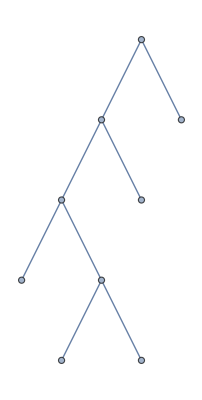
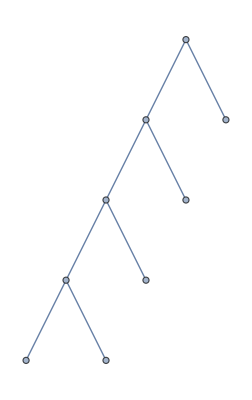

```mathematica
ExpressionGraph[#]&/@VertexList[{{"[◼]", "TwoWayRuleNestGraph"}}[x_∘ y_<->(y_∘x_)∘y_,a∘b,3,GraphLayout->"LayeredDigraphEmbedding",VertexShapeFunction->Automatic,AspectRatio->1/4,VertexStyle->_->FontSize->13]]
```

```mathematica
Table[{{"[◼]", "BranchialGraph"}}@{{"[◼]", "TwoWayRuleNestGraph"}}[x_<->y_∘ y_,a∘b,t,GraphLayout->"LayeredDigraphEmbedding",ImageSize->Medium,VertexShapeFunction->Automatic,AspectRatio->1/3,ImageSize->Scaled[0.85]],{t,2,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

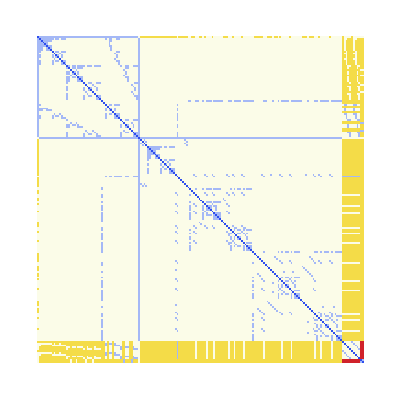

```mathematica
ArrayPlot[GraphDistanceMatrix[-Graphics-],ColorFunction->"TemperatureMap"]
```

```mathematica
{{"[◼]", "TwoWayRuleNestGraph"}}[x_∘ y_<->(y_∘x_)∘y_,a∘b,6,GraphLayout->"LayeredDigraphEmbedding",VertexShapeFunction->Automatic,AspectRatio->.5,VertexStyle->_->FontSize->13]
```

-Graphics-

```mathematica
Table[SimpleGraph@{{"[◼]", "TwoWayRuleNestGraph"}}[x_ <->y_∘y_,a∘b,t,GraphLayout->"LayeredDigraphEmbedding",ImageSize->Medium,VertexShapeFunction->Automatic,AspectRatio->1/4,VertexStyle->_->FontSize->13],{t,1,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
TreeMapAt[f, Tree[a,{Tree[b,{c,d}],e,f}], {1,1}]
```

-Graphics-

```mathematica
TreeMapAt[f, -Graphics-, {2}]
```

-Graphics-